## CP7: Systems of ODEs

This exercise demonstrates how Mathematica can be used to solve linear second-order ODEs and systems of ODEs

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Linear second-order ODEs

Entering a second-order ODE is very similar to what we have seen in CP3. We use the command D[] to calculate the first and second derivatives, and the command DSolveValue[] to solve the resulting differential equation. For a second-order ODE z''(t)=a·z'(t)+b·z(t) we need to define initial values for z(0)  and z'(0).
The commands Plot[] and ParametricPlot[] are used to create time plots and phase plots of a solution, respectively.

### Exercise 7-1

Calculate and plot the solution of the following second-order differential equations for initial values z(0)=2 and dz/dt(0)=1:

(a)  (ⅆ^2 z)/(ⅆ t^2)=1/2·ⅆz/ⅆt+3/16·z

```mathematica
init={z[0]==2, z'[0]==1}
```

{z[0]==2,z'[0]==1}

```mathematica
eq1=D[z[t],{t,2}]==1/2*D[z[t],t]+3/16*z[t]
```

z''[t]==(3 z[t])/16+z'[t]/2

```mathematica
charEq1=λ^2-1/2*λ-3/16;
l1 = Flatten[SolveValues[charEq1==0,λ]]
genSol1[A_,B_,t_]:=A*Exp[l1[[1]]*t]+B*Exp[l1[[2]]*t]
dGenSol1[A_, B_,t_]:=Derivative[0,0,1][genSol1][A, B,t]
{a1, b1}=Flatten[SolveValues[genSol1[A,B,0]==2&& dGenSol1[A, B, 0]==1,{A,B}]]
genSol1[a1, b1, t] // Simplify
```

{-1/4,3/4}

{1/2,3/2}

1/2 ⅇ^(-t/4) (1+3 ⅇ^t)

```mathematica
sol1=DSolveValue[{eq1, init}, z[t],t]
```

1/2 ⅇ^(-t/4) (1+3 ⅇ^t)

```mathematica
Plot[sol1,{t,-100,100}, AxesLabel->{"t", "z"}]
```

-Graphics-

```mathematica
Characteristic
```

(b)  (ⅆ^2 z)/(ⅆ t^2)=-2·ⅆz/ⅆt-2·z

```mathematica
init={z[0]==2, z'[0]==1};
eq2=D[z[t], {t,2}]==-2D[z[t],t]-2z[t]
```

z''[t]==-2 z[t]-2 z'[t]

```mathematica
charEq2=λ^2+2λ+2;
l2=Flatten[SolveValues[charEq2==0, λ]]
genSol2[A_,B_,t_]:=A*Exp[l2[[1]]*t]+B*Exp[l2[[2]]*t]
dGenSol2[A_,B_,t_]:=Derivative[0,0,1][genSol2][A, B, t]
{a2, b2}=Flatten[SolveValues[genSol2[A,B,0]==2 && dGenSol2[A, B, 0]==1,{A,B}]]
genSol2[a2, b2, t] //ComplexExpand // Simplify
```

{-1-ⅈ,-1+ⅈ}

{1+(3 ⅈ)/2,1-(3 ⅈ)/2}

ⅇ^-t (2 Cos[t]+3 Sin[t])

```mathematica
sol2=DSolveValue[{eq2, init}, z[t],t]
```

ⅇ^-t (2 Cos[t]+3 Sin[t])

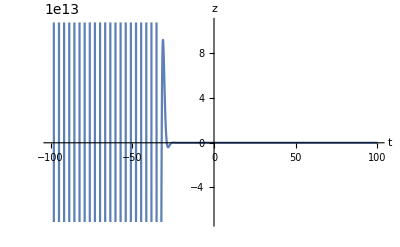

```mathematica
Plot[sol2,{t,-100,100}, AxesLabel->{"t", "z"}]
```

### Exercise 7-2

Calculate and plot the solution of the following linear systems of differential equations for initial values x(0)=2 and y(0)=0:

(a)  ⅆx/ⅆt=1/4 x+1/2 y, ⅆy/ⅆt=1/2 x+1/4 y

```mathematica
init={x[0]==x0, y[0]==y0};
x0=2; y0=0;
init
```

{x[0]==2,y[0]==0}

```mathematica
sys1={D[x[t],t]==1/4*x[t]+1/2*y[t],
D[y[t],t]==1/2*x[t]+1/4*y[t]}
```

{x'[t]==x[t]/4+y[t]/2,y'[t]==x[t]/2+y[t]/4}

{x[0]==2,y[2]==0}

```mathematica
mA={{1/4,1/2}, {1/2,1/4}};
MatrixForm[mA]
lSys1=Eigenvalues[mA]
lS1=Flatten[SolveValues[λ^2-Tr[mA]*λ+Det[mA]==0,λ]]
genSolSys1[A_,B_,t_]:=A*Exp[lS1[[1]]*t]+B*Exp[lS1[[2]]*t]
dGenSolSys1[A_,B_,t_]:=Derivative[0,0,1][genSolSys1][A,B,t]
{aS1,bS1}=Flatten[SolveValues[genSolSys1[A,B,0]==x0 && dGenSolSys1[A,B,0]==1/4*x0+1/2*y0,{A,B}]]
{cS1,dS1}=Flatten[SolveValues[genSolSys1[c,d,0]==y0 && dGenSolSys1[c,d,0]==1/2*x0+1/4*y0,{c,d}]]
xS1=genSolSys1[aS1, bS1, t]//Simplify
yS1=genSolSys1[cS1, dS1,t]//Simplify
```

(1/4 | 1/2
1/2 | 1/4)

{3/4,-1/4}

{-1/4,3/4}

{1,1}

{-1,1}

ⅇ^(-t/4) (1+ⅇ^t)

ⅇ^(-t/4) (-1+ⅇ^t)

```mathematica
solS1=DSolveValue[{sys1, init}, {x[t],y[t]},t]
```

{ⅇ^(-t/4) (1+ⅇ^t),ⅇ^(-t/4) (-1+ⅇ^t)}

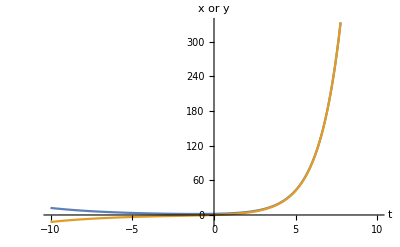

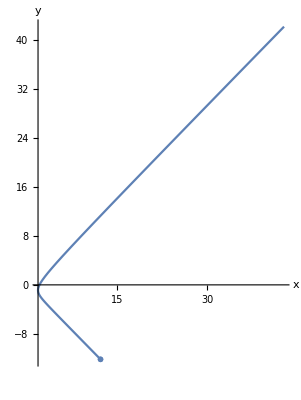

```mathematica
Plot[solS1,{t,-10,10},AxesLabel->{"t", "x or y"}]
phase=ParametricPlot[solS1, {t, -10,5}, AxesLabel->{"x","y"}, PlotRange->Full];
initPoint=ListPlot[{{solS1[[1]]/.t->-10, solS1[[2]]/.t->-10}}, PlotMarkers->{Red}];
Show[phase, initPoint]
```

(b)  ⅆx/ⅆt=-x-y, ⅆy/ⅆt=x-y

```mathematica
sys2={D[x[t],t]==-x[t]-y[t], D[y[t],t]==x[t]-y[t]}
x0=2; y0=0;
init
```

{x'[t]==-x[t]-y[t],y'[t]==x[t]-y[t]}

{x[0]==2,y[0]==0}

```mathematica
mA={{-1,-1},{1,-1}};
MatrixForm[mA]
solSys2=Eigenvalues[mA]
solS2=Flatten[SolveValues[λ^2-Tr[mA]*λ+Det[mA]==0,λ]]
genSolSys2[A_,B_,t_]:=A*Exp[solS2[[1]]*t]+B*Exp[solS2[[2]]*t]
dGenSolSys2[A_,B_,t_]:=Derivative[0,0,1][genSolSys2][A,B,t]
{aS2,bS2}=Flatten[SolveValues[genSolSys2[A,B,0]==x0 && dGenSolSys2[A,B,0]==-x0-y0,{A,B}]]
{cS2,dS2}=Flatten[SolveValues[genSolSys2[c,d,0]==y0 && dGenSolSys2[c,d,0]==x0-y0,{c,d}]]
xS2=genSolSys2[aS2,bS2,t]//ComplexExpand//Simplify
yS2=genSolSys2[cS2,dS2,t]//ComplexExpand//Simplify
```

(-1 | -1
1 | -1)

{-1+ⅈ,-1-ⅈ}

{-1-ⅈ,-1+ⅈ}

{1,1}

{ⅈ,-ⅈ}

2 ⅇ^-t Cos[t]

2 ⅇ^-t Sin[t]

```mathematica
sol2=DSolveValue[{sys2, init}, {x[t],y[t]},t]
```

{2 ⅇ^-t Cos[t],2 ⅇ^-t Sin[t]}

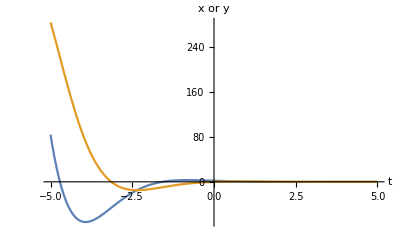

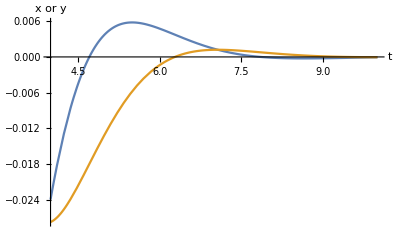

```mathematica
Plot[sol2, {t, -5,5}, AxesLabel->{"t", "x or y"}, PlotRange->All]
Plot[sol2, {t, 4,10}, AxesLabel->{"t", "x or y"}, PlotRange->All]
```

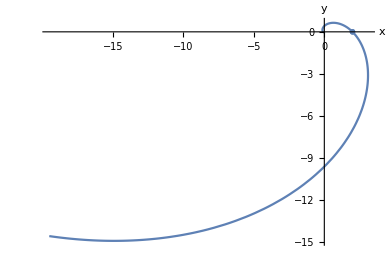

```mathematica
phase=ParametricPlot[sol2, {t, -2.5, 5}, AxesLabel->{"x", "y"}, PlotRange->Full];
initPoint=ListPlot[{{sol2[[1]]/.t->0, sol2[[2]]/.t->0}}, PlotMarkers->Red];
Show[phase, initPoint]
```

This system oscillate continuously but appears to eventually converge to zero.

### Exercise 7-3

Hooke’s Law can be described by the second-order differential equation:  m·(ⅆ^2 x)/(ⅆ t^2)=-c·ⅆx/ⅆt-k·x
Consider this equation for specific conditions m=1 and k=4 and the following three scenarios:
(i) c=0 (no friction)
(ii) c=2 (low friction)
(iii) c=5 (heavy friction)

(a) Solve the equation for each scenario and initial conditions x(0)=2  and dx/dt(0)=0

```mathematica
init={x[0]==2, x'[0]==0}
hooke[c_]:=D[x[t], {t,2}]==-c*D[x[t],t]-4*x[t]
xs=Table[DSolveValue[{hooke[c], init}, x[t], t],{c, {0,2,5}}]
```

{x[0]==2,x'[0]==0}

{2 Cos[2 t],2/3 ⅇ^-t (3 Cos[√3 t]+√3 Sin[√3 t]),2/3 ⅇ^(-4 t) (-1+4 ⅇ^(3 t))}

(b) Plot all three scenarios in one graph. What can you conclude?

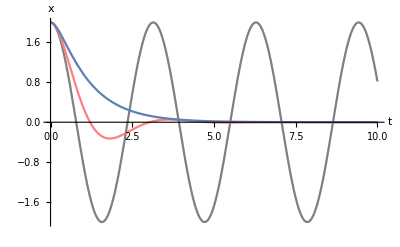

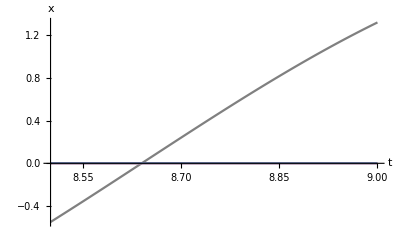

```mathematica
Plot[xs, {t, 0,10}, AxesLabel->{"t", "x"}, PlotRange->Full, PlotStyle->{Gray, Pink, ColorData[97, 1]}]
Plot[xs, {t, 8.5,9}, AxesLabel->{"t", "x"}, PlotRange->Full, PlotStyle->{Gray, Pink, ColorData[97, 1]}]
```

Without friction, oscillations between x=-2 and x=2. The heavier the friction, the faster the oscillations die out and x converges faster to zero.

### Exercise 7-4

In this exercise, we compare a system of differential equations to a system of recurrence (difference) equations
differential equations:  ⅆx/ⅆt=-0.1x+y, ⅆy/ⅆt=0.2x-0.2y
Recurrence equations:  x(t+1)=-0.1x(t)+y(t), y(t+1)=0.2x(t)-0.2y(t)

(a) Calculate a general solution for both systems with initial values x(0)=y(0)=1. If Mathematica cannot solve the system, consider writing the decimal values in terms of fractions, i.e. 1/5 instead of 0.2. When using fractions, Mathematica tries to get an exact result, whereas when you give Mathematica decimal values, it will use floating point arithmetic, i.e. it will use numerical procedures that can lead to inaccurate results, because they work with limited precision.

```mathematica
mA={{-1/10, 1},{1/5,-1/5}};
MatrixForm[mA]
ode={D[x[t],t]==mA[[1,1]]*x[t]+mA[[1,2]]*y[t],
D[y[t],t]==mA[[2,1]]*x[t]+mA[[2,2]]*y[t]}
re={x[t+1]==mA[[1,1]]*x[t]+mA[[1,2]]*y[t],
y[t+1]==mA[[2,1]]*x[t]+mA[[2,2]]*y[t]}
init={x[0]==1, y[0]==1}
```

(-1/10 | 1
1/5 | -1/5)

{x'[t]==-x[t]/10+y[t],y'[t]==x[t]/5-y[t]/5}

{x[1+t]==-x[t]/10+y[t],y[1+t]==x[t]/5-y[t]/5}

{x[0]==1,y[0]==1}

```mathematica
solODE=DSolveValue[{ode, init}, {x[t],y[t]},t]//Simplify
solRE=RSolveValue[{re, init}, {x[t], y[t]},t]//Simplify
```

{1/3 ⅇ^(-3 t/5) (-2+5 ⅇ^(9 t/10)),1/3 ⅇ^(-3 t/5) (1+2 ⅇ^(9 t/10))}

{3^(-1+t) 10^-t (5+(-2)^(1+t)),3^(-1+t) 10^-t (2+(-2)^t)}

(b)  Plot the solutions for both systems, and describe what happens for t -> ∞. Can you explain the different behaviour of the two types of systems?

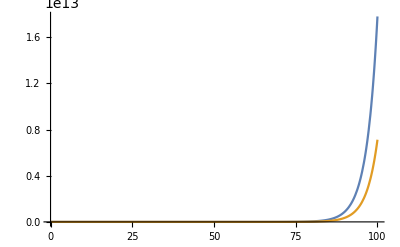

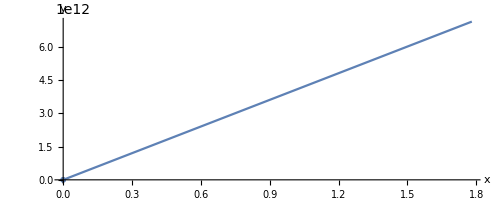

```mathematica
time=Plot[solODE, {t, 0,100}, PlotRange->Full]
phase=ParametricPlot[solODE, {t, 0, 100}, PlotRange->Full, AxesLabel->{"x", "y"}];
initPoint=ListPlot[{{solODE[[1]]/.t->0, solODE[[2]]/.t->0}}, PlotMarkers->Red];
Show[phase, initPoint]
```

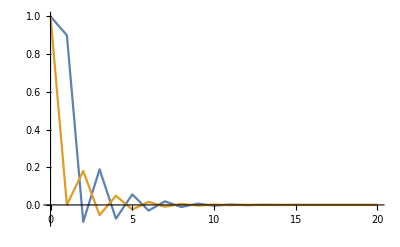

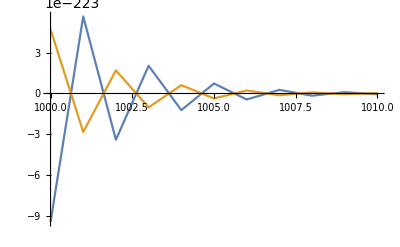

```mathematica
DiscretePlot[{solRE[[1]], solRE[[2]]}, {t, 0,20}, Joined->True, Filling->None,PlotRange->All]
DiscretePlot[{solRE[[1]], solRE[[2]]}, {t, 1000,1010}, Joined->True, Filling->None,PlotRange->All]
```

```mathematica
points=RecurrenceTable[{re, init}, {x,y}, {t,0,5}]
points=Table[solRE/.t->i, {i, 0,5}]
```

{{1,1},{9/10,0},{-9/100,9/50},{189/1000,-27/500},{-729/10000,243/5000},{5589/100000,-243/10000}}

{{1,1},{9/10,0},{-9/100,9/50},{189/1000,-27/500},{-729/10000,243/5000},{5589/100000,-243/10000}}

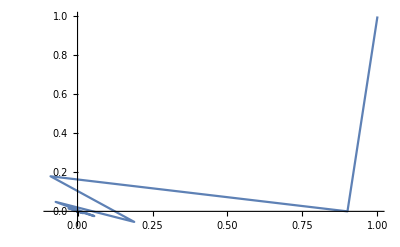

```mathematica
points=RecurrenceTable[{re, init}, {x,y}, {t,0,100}];
ListLinePlot[points, PlotRange->Full]
```

The ODE system diverged to infinity, because the positive exponential diverges to infinity over time. 
In the discrete Recurrence, system both terms converge to zero, hence the solution will converge to zero over time. Although, both terms keep oscillating over time.
We see that although both systems share the same matrix A, and thus, same eigenvalues, their solutions are completely different from each other, each with different behaviour.